```mathematica
ClearAll[P12,P15,P23,P24,P27,P37,P38,P46,P54,P56,P68,P71,P77,P81,P88,p,sum,k,storep,phi,pi,Dphi]
```

```mathematica
nmax=20000;k=1;
```

```mathematica
P12=RandomReal[];
P15=1-P12;
P23=RandomReal[];
P24=RandomReal[{0,1-P23}];
P27=1-P23-P24;
P37=RandomReal[];
P38=1-P37;
P46=1;
P54=RandomReal[];
P56=1-P54;
P68=1;
P71=0.15;
P77=1-P71;
P81=0.15;
P88=1-P81;
p=({{0, P12, 0, 0, P15, 0, 0, 0}, {0, 0, P23, P24, 0, 0, P27, 0}, {0, 0, 0, 0, 0, 0, P37, P38}, {0, 0, 0, 0, 0, P46, 0, 0}, {0, 0, 0, P54, 0, P56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, P68}, {P71, 0, 0, 0, 0, 0, P77, 0}, {P81, 0, 0, 0, 0, 0, 0, P88}});
pi=Re[Eigenvectors[Transpose[p],1]];
If[Re[Part[pi,1,8]]<0,pi=pi*(-1)];
phi[0]=Re[Part[pi,1,8]]/(Re[Part[pi,1,7]]+0.01)
```

1.86841

```mathematica
For[i=1,i<nmax,i=i+1,{P12=RandomReal[];
P15=1-P12;
P23=RandomReal[];
P24=RandomReal[{0,1-P23}];
P27=1-P23-P24;
P37=RandomReal[];
P38=1-P37;
P46=1;
P54=RandomReal[];
P56=1-P54;
P68=1;
P71=0.15;
P77=1-P71;
P81=0.15;
P88=1-P81;p=({{0, P12, 0, 0, P15, 0, 0, 0}, {0, 0, P23, P24, 0, 0, P27, 0}, {0, 0, 0, 0, 0, 0, P37, P38}, {0, 0, 0, 0, 0, P46, 0, 0}, {0, 0, 0, P54, 0, P56, 0, 0}, {0, 0, 0, 0, 0, 0, 0, P68}, {P71, 0, 0, 0, 0, 0, P77, 0}, {P81, 0, 0, 0, 0, 0, 0, P88}});
pi=Re[Eigenvectors[Transpose[p],1]];If[Re[Part[pi,1,8]]<0,pi=pi*(-1)];phi[i]=Re[Part[pi,1,8]]/(Re[Part[pi,1,7]]+0.01);Dphi=phi[i]-phi[i-1];
r=Exp[-Dphi/2];z=RandomReal[];
If[r>z,{storep[k]=p,k=k+1},indeterminate]}]
```

```mathematica
k
```

12447

```mathematica
sum=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
For[j=1,j<k,j=j+1,sum=sum+storep[j]];
```

```mathematica
PFinal=sum/(k-1) ;
pifinal=Re[Eigenvectors[Transpose[PFinal],1]];
F12=Part[PFinal,1,2]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,1]];
F15=Part[PFinal,1,5]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,1]];
F23=Part[PFinal,2,3]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,2]];
F24=Part[PFinal,2,4]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,2]];
F27=Part[PFinal,2,7]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,2]];
F37=Part[PFinal,3,7]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,3]];
F38=Part[PFinal,3,8]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,3]];
F46=Part[PFinal,4,6]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,4]];
F54=Part[PFinal,5,4]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,5]];
F56=Part[PFinal,5,6]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,5]];
F68=Part[PFinal,6,8]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,6]];
F71=Part[PFinal,7,1]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,7]];
F77=Part[PFinal,7,7]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,7]];
F81=Part[PFinal,8,1]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,8]];
F88=Part[PFinal,8,8]*Abs[Part[Re[Eigenvectors[Transpose[PFinal],1]],1,8]];
```

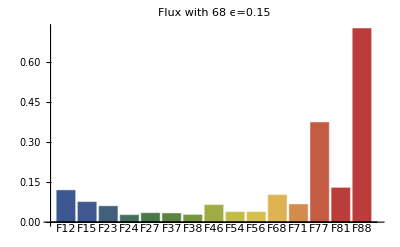

```mathematica
BarChart[{F12,F15,F23,F24,F27,F37,F38,F46,F54,F56,F68,F71,F77,F81,F88},ChartLabels->{"F12","F15","F23","F24","F27","F37","F38","F46","F54","F56","F68","F71","F77","F81","F88"},ChartStyle->"DarkRainbow",PlotLabel->"Flux with 68 ϵ=0.15"]
```